```mathematica
(*Data*)
bigboifunc[Nn_,e_]:=(
μ=3.9877848 10^14;
Mp=1000;
l=100000;
a=6870000;
τ = 0;
Mt = 0;
ranget = 3000000;
animationrate = 500;(*dt per second*)

psiQ =τ ;

(*Position vectorc and linear kinetic energy (translation of centre of mass)*)
rm[t] = ({{rc[t] Cos[θ[t]]}, {rc[t] Sin[θ[t]]}, {0}});
rp1[t]=rm[t]+({{l Cos[α[t]] Cos[ψ[t]+θ[t]]}, {l Cos[α[t]] Sin[ψ[t]+θ[t]]}, {l Sin[α[t]]}});
rp2[t]=rm[t]-({{l Cos[α[t]] Cos[ψ[t]+θ[t]]}, {l Cos[α[t]] Sin[ψ[t]+θ[t]]}, {l Sin[α[t]]}});
rt[t] =(2l)/(Nn+1) ({{Cos[α[t]] Cos[ψ[t]+θ[t]]}, {Cos[α[t]] Sin[ψ[t]+θ[t]]}, {Sin[α[t]]}}); 

rm'[t]=D[rm[t], t];
rp1'[t]=D[rp1[t], t];
rp2'[t]=D[rp2[t], t];

Subscript[T, lin]=1/2 (2*Mp+Mt) (rc'[t]^2+rc[t]^2 θ'[t]^2);

(*Rotational kinetic energy (rotation of system about centre of mass)*)
ω[t]=({{γ'[t]+(θ'[t]+ψ'[t])Sin[α[t]]}, {-Cos[γ[t]] α'[t]+Cos[α[t]] Sin[γ[t]] (θ'[t]+ψ'[t])}, {Sin[γ[t]] α'[t]+Cos[α[t]] Cos[γ[t]] (θ'[t]+ψ'[t])}});

ⅈp=({{0, 0, 0}, {0, 2 Mp l^2, 0}, {0, 0, 2 Mp l^2}})  ;
ⅈtether=If[OddQ[Nn],
(*odd number of points, sum of moments of pairs of point masses at ±nδl from centre*)
Sum[({{0, 0, 0}, {0, 2 Mt/Nn ((2 n l)/(Nn+1))^2, 0}, {0, 0, 2 Mt/Nn ((2 n l)/(Nn+1))^2}}),{n,1,(Nn-1)/2}],
(*even number of points, sum of moments of pairs of point masses at ±(2n-1)/2 δl from centre, (1/2,3/2,5/2...)*)
Sum[({{0, 0, 0}, {0, 2 Mt/Nn (((2n-1) l)/(Nn+1))^2, 0}, {0, 0, 2 Mt/Nn (((2n-1) l)/(Nn+1))^2}}),{n,1,Nn/2}]];
Subscript[ⅈ, 123] = ⅈp+ⅈtether;
Subscript[T, rot]=1/2 Transpose[ω[t]].Subscript[ⅈ, 123].ω[t];

T=Subscript[T, lin]+Subscript[T, rot];

(*potential energy*)
Up1=-(μ Mp)/(√(Transpose[rp1[t]].rp1[t]));
Up2=-(μ Mp)/(√(Transpose[rp2[t]].rp2[t]));
Utether=If[OddQ[Nn],
(*sum of potentials for odd number of points (sum from 0 first to get center mass)
position vector is r(centre) + vector in direction from centre to payload, with magnitude length/number of points+1 *)
Sum[(-(μ Mt/Nn)/(√(Transpose[rm[t]+n*rt[t]].(rm[t]+n*rt[t])))),{n,0,(Nn-1)/2}]+Sum[(-(μ Mt/Nn)/(√(Transpose[rm[t]-n*rt[t]].(rm[t]-n*rt[t])))),{n,1,(Nn-1)/2}],
(*sum of potentials for even number of points, same idea but vector is 1/2, 3/2, 5/2 * length/Nn+1 due to symmetry around center *)
Sum[(-(μ Mt/Nn)/(√(Transpose[rm[t]+(2n-1)/2*rt[t]].(rm[t]+(2n-1)/2*rt[t])))),{n,1,Nn/2}]+Sum[(-(μ Mt/Nn)/(√(Transpose[rm[t]-(2n-1)/2*rt[t]].(rm[t]-(2n-1)/2*rt[t])))),{n,1,Nn/2}]];
V=Up1+Up2 +Utether;
L=T-V;
eqn1=Simplify[D[D[T, ψ'[t]], t]-D[T, ψ[t]]]+ D[V, ψ[t]]-psiQ;
eqn2=Simplify[D[D[T, α'[t]], t]-D[T, α[t]]]+ D[V, α[t]];
eqn3 = Simplify[D[D[L, θ'[t]], t]-D[L, θ[t]]];
eqn4 =Simplify[D[D[T, rc'[t]], t]-D[T, rc[t]]]+ D[V, rc[t]];
eqn5 = Cos[α[t]] α'[t] (θ'[t]+ψ'[t])+γ''[t]+Sin[α[t]] (θ''[t]+ψ''[t]);
(*initial conditions*)
alpha0 = 0;
alphadsh0 = 0 ;
psi0 = Pi/3;
psidsh0 =0;
gamma0=0;
r0 = a (1-e);
rdsh0 = 0;
theta0 = 0;
thetadsh0=1/r0*√((μ (1+e))/(a (1-e)))  ;

system=NDSolve[{eqn1[[1]][[1]]==0,eqn2[[1]][[1]]==0,eqn3[[1]][[1]]==0,eqn4[[1]][[1]]==0,eqn5==0,
α[0]==alpha0,α'[0]==alphadsh0,ψ[0]==psi0,ψ'[0]==psidsh0, θ[0] == theta0,θ'[0]==thetadsh0,rc[0] == r0,rc'[0]==0,γ[0]==gamma0,γ'[0]==0},
{ψ,α,θ,rc,γ},{t,0,ranget},
MaxSteps->∞,AccuracyGoal->Automatic,PrecisionGoal->10,Method->{"EquationSimplification"->"Residual"}];
gammas[t_]:=γ[t]/.system[[1]];
alphas[t_]:=α[t]/.system[[1]];
psis[t_]:=ψ[t]/.system[[1]];
rs[t_]:=rc[t]/.system[[1]];
rvs[t_]:=rc'[t]/.system[[1]];
thetas[t_]:=θ[t]/.system[[1]];
gammadshs[t_]:=Evaluate[γ'[t]/.system[[1]]];
thetadshs[t_]:=Evaluate[θ'[t]/.system[[1]]];
alphadshs[t_]:=Evaluate[α'[t]/.system[[1]]];
psidshs[t_]:=Evaluate[ψ'[t]/.system[[1]]];


rm22[t_] := ({{rs[t] Cos[thetas[t]]}, {rs[t] Sin[thetas[t]]}, {0}});
rp122[t_]:=rm22[t]+({{l Cos[alphas[t]] Cos[psis[t]+thetas[t]]}, {l Cos[alphas[t]] Sin[psis[t]+thetas[t]]}, {l Sin[alphas[t]]}});
rp222[t_]:=rm22[t]-({{l Cos[alphas[t]] Cos[psis[t]+thetas[t]]}, {l Cos[alphas[t]] Sin[psis[t]+thetas[t]]}, {l Sin[alphas[t]]}});
rt22[t_] :=(2l)/(Nn+1) ({{Cos[alphas[t]] Cos[psis[t]+thetas[t]]}, {Cos[alphas[t]] Sin[psis[t]+thetas[t]]}, {Sin[alphas[t]]}}); 

Tlin22[t_]:=1/2 (2*Mp+Mt) ( rvs[t]^2+rs[t]^2 thetadshs[t]^2);

omegas[t_]:= ({{gammadshs[t]+(thetadshs[t]+psidshs[t])Sin[alphas[t]]}, {-Cos[gammas[t]] alphadshs[t]+Cos[alphas[t]] Sin[gammas[t]] (thetadshs[t]+psidshs[t])}, {Sin[gammas[t]] alphadshs[t]+Cos[alphas[t]] Cos[gammas[t]] (thetadshs[t]+psidshs[t])}});

Trot[t_] := 1/2 Transpose[omegas[t]].Subscript[ⅈ, 123].omegas[t];
T22[t_]:=(Tlin22[t]+Trot[t])[[1]][[1]];
discretepotensh[t_]:=If[OddQ[Nn],
(*sum of potentials for odd number of points (sum from 0 first to get center mass)
position vector is r(centre) + vector in direction from centre to payload, with magnitude length/number of points+1 *)
Sum[(-(μ Mt/Nn)/(√(Transpose[rm22[t]+n*rt22[t]].(rm22[t]+n*rt22[t])))),{n,0,(Nn-1)/2}]+Sum[(-(μ Mt/Nn)/(√(Transpose[rm22[t]-n*rt22[t]].(rm22[t]-n*rt22[t])))),{n,1,(Nn-1)/2}],
(*sum of potentials for even number of points, same idea but vector is 1/2, 3/2, 5/2 * length/Nn+1 due to symmetry around center *)
Sum[(-((μ Mt/Nn)/(√(Transpose[rm22[t]+(2n-1)/2*rt22[t]].(rm22[t]+(2n-1)/2*rt22[t]))))),{n,1,Nn/2}]+Sum[(-((μ Mt/Nn)/(√(Transpose[rm22[t]-(2n-1)/2*rt22[t]].(rm22[t]-(2n-1)/2*rt22[t]))))),{n,1,Nn/2}]];
p1potensh[t_]:=-(μ Mp)/(√(Transpose[rp122[t]].rp122[t]));
p2potensh[t_]:=-(μ Mp)/(√(Transpose[rp222[t]].rp222[t]));
potensh[t_]:=discretepotensh[t][[1]][[1]]+p1potensh[t][[1]][[1]]+p2potensh[t][[1]][[1]];
energy[t_]:= T22[t]+potensh[t]

)
```

```mathematica
points={};
maxes = {};
mins ={};
avrgs={};
errors={};
Do[Print[n];
bigboifunc[n];
mins=Append[mins,{n,MinValue[{energy[t],0<t<ranget},t]}];
errors=Append[errors,{n, MaxValue[{energy[t],0<t<ranget},t]-MinValue[{energy[t],0<t<ranget},t]}],

{n,1,50}]
```

1

2

3

4

$Aborted

```mathematica
ListPlot[mins,PlotMarkers->{•,15},PlotLabel->Style["Tether Mass Discretisation",FontFamily->"Liberation Serif",35],AxesLabel->{Style["N",FontFamily->"Liberation Serif"],Style["Total Energy (J)",FontFamily->"Liberation Serif"]},LabelStyle->Directive[Black,18,FontFamily->"Liberation Serif"],ImageSize->{1080},PlotStyle->Black,PlotRange->All]
ListPlot[errors,PlotMarkers->{•,15},PlotLabel->Style["Energy Range",FontFamily->"Liberation Serif",35],AxesLabel->{Style["N",FontFamily->"Liberation Serif"],Style["Energy (J)",FontFamily->"Liberation Serif"]},LabelStyle->Directive[Black,18,FontFamily->"Liberation Serif"],ImageSize->{1080},PlotStyle->Black]
```

Part::partd: Part specification 0⟦1⟧ is longer than depth of object.

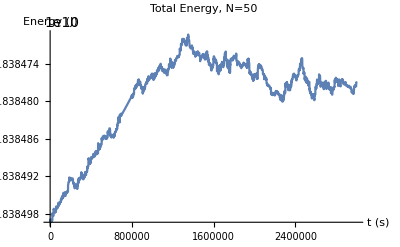

```mathematica
Plot[energy[t],{t,0,ranget},PlotLabel->Style["Total Energy, N=50",FontFamily->"Liberation Serif",35],AxesLabel->{Style["t (s)",FontFamily->"Liberation Serif"],Style["Energy (J)",FontFamily->"Liberation Serif"]},LabelStyle->Directive[Black,18,FontFamily->"Liberation Serif"],ImageSize->{1080},FrameTicks->False]
```

```mathematica
bigboifunc[1,0.8]
T22[0]+
potensh[0]
```

-5.48901×10^10

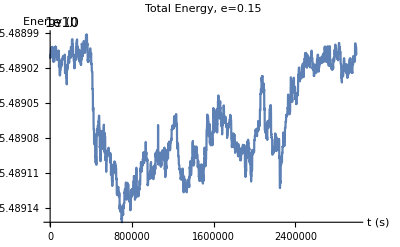

```mathematica
tickFormat[xmin_,xmax_,digits_,divisions_: 10]:=Function[tickNumber,{tickNumber,PaddedForm[Round[tickNumber,0.01],{Max@(Length@IntegerDigits@IntegerPart[#]&/@(10^digits {xmin,xmax})),digits}]}]/@FindDivisions[{xmin,xmax},divisions];

Plot[energy[t],{t,0,3*10^6},PlotLabel->Style["Total Energy, e=0.15",FontFamily->"Liberation Serif",35],AxesLabel->{Style["t (s)",FontFamily->"Liberation Serif"],Style["Energy (J)",FontFamily->"Liberation Serif"]},LabelStyle->Directive[Black,18,FontFamily->"Liberation Serif"],ImageSize->{1080},FrameTicks->(tickFormat[#1,#2,20,20]&)]
```

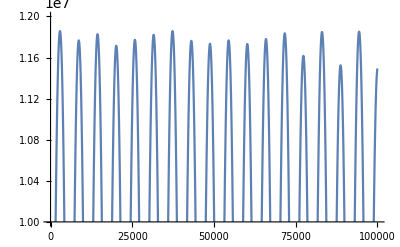

```mathematica
Plot[rs[t],{t,0,ranget},PlotRange->{1*10^7,1.2*10^7}]
```